# ΛCDM Dynamics

In  this  notebook, a  dynamical  systems  analysis  of  the LambdaCDM model  is  completed.
   
Copyright  ©  2024  Molly  Burkmar

This  program  is  free  software : you  can  redistribute  it  and/or  modify  it  under  the  terms  of  the  GNU  General  Public  License  as  published  by  the  Free  Software  Foundation, either  version  3  of  the  License, or  (at  your  option)  any  later  version . This  program  is  distributed  in  the  hope  that  it  will  be  useful, but  WITHOUT  ANY  WARRANTY; without  even  the  implied  warranty  of  MERCHANTABILITY  or  FITNESS  FOR  A  PARTICULAR  PURPOSE . See  the  GNU  General  Public  License  for  more  details . You  should  have  received  a  copy  of  the  GNU  General  Public  License  along  with  this  program . If  not, see  https://www.gnu.org/licenses/. 

The  author  can  be  contacted  at  molly.burkmar@port.ac.uk

## General System of Equations

Here, we plot the dynamics of the 3D system, with the ODEs for the Hubble function, cold dark matter and radiation, for general initial conditions, i.e. for any Y0, Z0 and R0.

### Set-up

```mathematica
(*Load MaTeX to typeset axis labels using LaTeX*)
<<MaTeX`
```

```mathematica
(*Define a format style for the Z-Y-R phase spaces*)
PhaseSpaceFormat3D={AxesLabel->{MaTeX["Z",FontSize->20],MaTeX["Y",FontSize->20],MaTeX["R",FontSize->20]},Ticks->{{0.,0.5,1.0},{-1,-0.5,0.,0.5,1.0},{0.,0.5,1.0}},PlotRange->{{0,1},{-1,1},{0,1}},ImageSize->{600,400},PlotRangePadding->{0.08,0.08,0.08},BaseStyle->{FontFamily->"CMU Serif",FontSize->20}};
```

### 3D Phase Space

#### Non-Compact Variables

```mathematica
(*Define the system of equations in terms of dimensionless parameters*)
(* y = H/Sqrt[Λ], z = ρm/Λ, r = ρr/Λ *)
dey:=y'=-y^2-(1/6)*(z+2*r-2)
dez:=z'=-3*y*z
der:=r'=-4*y*r
```

```mathematica
(*Find the fixed points of the full system*)
FPs=Solve[{dez==0,dey==0,der==0},{z,y,r}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{y→0,r→(2-z)/2},{z→0,y→-1/(√3),r→0},{z→0,y→1/(√3),r→0}}

```mathematica
(*Remove the arrows from the fixed points*)
FP3D[1]={z,y/.FPs[[1,1]],r/.FPs[[1,2]]};
FP3D[2]={z/.FPs[[2,1]],y/.FPs[[2,2]],r/.FPs[[2,3]]};
FP3D[3]={z/.FPs[[3,1]],y/.FPs[[3,2]],r/.FPs[[3,3]]};
```

```mathematica
(*Put the fixed points into a table*)
FPTable=Table[FP3D[i],{i,1,3}]
```

{{z,0,(2-z)/2},{0,-1/(√3),0},{0,1/(√3),0}}

```mathematica
(*Find the 3D Jacobian matrix for the general system of equations. D[] differentiates each expression*)
J=Simplify[{{D[dez,z],D[dez,y],D[dez,r]}, {D[dey,z],D[dey,y],D[dey,r]},{D[der,z],D[der,y],D[der,r]}}];
J//MatrixForm
```

(-3 y | -3 z | 0
-1/6 | -2 y | -1/3
0 | -4 r | -4 y)

```mathematica
(*Subtract λI from J and find its determinant*)
J-λ*IdentityMatrix[3]//MatrixForm
```

(-3 y-λ | -3 z | 0
-1/6 | -2 y-λ | -1/3
0 | -4 r | -4 y-λ)

```mathematica
Det[J-λ*IdentityMatrix[3]]
```

4 r y-24 y^3+2 y z+(4 r λ)/3-26 y^2 λ+(z λ)/2-9 y λ^2-λ^3

```mathematica
(*Find the Jacobian and eigenvalues for each fixed point*)
fpTable=TableForm[Table[{FPTable[[i]]//MatrixForm,Simplify[J/.{z->FPTable[[i,1]],y->FPTable[[i,2]],r->FPTable[[i,3]]}]//MatrixForm,Simplify[Eigenvalues[J/.{z->FPTable[[i,1]],y->FPTable[[i,2]],r->FPTable[[i,3]]}]]//MatrixForm},{i,1,3}],TableHeadings->{None,{"Fixed Point", "Jacobian","Eigenvalues"}}]
```

Fixed Point | Jacobian | Eigenvalues
(z
0
(2-z)/2) | (0 | -3 z | 0
-1/6 | 0 | -1/3
0 | 2 (-2+z) | 0) | (0
-(√(8-z))/(√6)
(√(8-z))/(√6))
(0
-1/(√3)
0) | (√3 | 0 | 0
-1/6 | 2/(√3) | -1/3
0 | 0 | 4/(√3)) | (4/(√3)
√3
2/(√3))
(0
1/(√3)
0) | (-√3 | 0 | 0
-1/6 | -2/(√3) | -1/3
0 | 0 | -4/(√3)) | (-4/(√3)
-√3
-2/(√3))

#### Compact Variables

```mathematica
(*Define the system of equations in terms of compact variables*)
deY:=Y'=-Y^2*(1-Y^2)^(1/2)-(1/6)*(1-Y^2)^(3/2)*(Z/(1-Z)+2*R/(1-R)-2)
deZ:=Z'=-3*Y*Z*(1-Z)/(Sqrt[1-Y^2])
deR:=R'=-4*Y*R*(1-R)/(Sqrt[1-Y^2])
```

```mathematica
(*Find the fixed points of the compact 3D system*)
FP3DCompact=Solve[{deZ==0,deY==0,deR==0},{Z,Y,R}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{Y→0,R→(-2+3 Z)/(-4+5 Z)},{Z→0,Y→-1/2,R→0},{Z→0,Y→1/2,R→0},{Z→0,Y→0,R→1/2},{Z→2/3,Y→0,R→0}}

```mathematica
(*Plot the line of Einstein fixed points in the compact 3D phase space*)
ECompactLine=ParametricPlot3D[{Z,0,(-2+3 Z)/(-4+5 Z)},{Z,0,0.8},PlotStyle->Purple,PlotRange->{{0,1},{-1,1},{0,1}}];
```

```mathematica
(*Remove the arrows from the fixed points*)
FPCompact[1]={Z/.FP3DCompact[[2,1]],Y/.FP3DCompact[[2,2]],R/.FP3DCompact[[2,3]]};
FPCompact[2]={Z/.FP3DCompact[[3,1]],Y/.FP3DCompact[[3,2]],R/.FP3DCompact[[3,3]]};
FPCompact[3]={Z/.FP3DCompact[[4,1]],Y/.FP3DCompact[[4,2]],R/.FP3DCompact[[4,3]]};
FPCompact[4]={Z/.FP3DCompact[[5,1]],Y/.FP3DCompact[[5,2]],R/.FP3DCompact[[5,3]]};
```

```mathematica
(*Put the fixed points into a table*)
FPCompactTable3D=Table[FPCompact[i],{i,1,2}];
```

```mathematica
(*Plot the fixed points*)
FPPlotCompact3D=ListPointPlot3D[{FPCompactTable3D},PlotStyle->Black];
```

```mathematica
(*Plot the repellor and attractor singularities*)
Singularities3D=ListPointPlot3D[{{1,1,1},{1,-1,1}},PlotStyle->Black];
```

```mathematica
(*Plot the compact 3D phase space*)
StreamPlot3D[{deZ,deY,deR},{Z,0,0.999},{Y,-0.999,0.999},{R,0,0.999},StreamPoints->28]
```

-Graphics3D-

Although the phase space above shows the full range of dynamics, the phase space is clearer if we define R = R(Z), and then choose values of Z0, R0 and Y0 to plot the trajectories.

```mathematica
(*Express R in terms of Z*)
rofZ[crz_]=crz*(Z/(1-Z))^(4/3);
RofZ[crz_]=rofZ[crz]/(1+rofZ[crz])
```

(crz (Z/(1-Z))^(4/3))/(1+crz (Z/(1-Z))^(4/3))

```mathematica
(*Solve crz in terms of Z0 and R0*)
Simplify[Solve[RofZ[crz]==R0/.Z->Z0,crz]]
```

{{crz→-R0/((-1+R0) (-Z0/(-1+Z0))^(4/3))}}

```mathematica
(*Express R in terms of Z, Z0 and R0*)
RofZcrz[Z0_,R0_]=Simplify[RofZ[-R0/((-1+R0) (-Z0/(-1+Z0))^(4/3))]]
```

-(R0 (-Z/(-1+Z))^(4/3))/((-1+R0) (-Z0/(-1+Z0))^(4/3) (1-(R0 (-Z/(-1+Z))^(4/3))/((-1+R0) (-Z0/(-1+Z0))^(4/3))))

```mathematica
(*Define the Friedmann equation in terms of Y^2/(1-Y^2) to plot trajectories in the phase space*)
trajFriedmannZYR[Y0_,Z0_,R0_]:=1/3+Z/(3*(1-Z))+RofZcrz[Z0,R0]/(3*(1-RofZcrz[Z0,R0]))-((Z*(1-Z0))/(Z0*(1-Z)))^(2/3)*(1/3+Z0/(3*(1-Z0))+R0/(3*(1-R0))-Y0^2/(1-Y0^2))
```

```mathematica
(*Rearrange the above equation for Y*)
(*Note that when plotting the trajectories, +trajZYR and -trajZYR needs to be plotted as a Sqrt is taken and Mathematica outputs the + solution only*)
trajZYR[Y0_,Z0_,R0_]=Sqrt[trajFriedmannZYR[Y0,Z0,R0]/(1+trajFriedmannZYR[Y0,Z0,R0])];
```

```mathematica
(*Plot trajectories with different values of Z0, Y0 and R0*)
```

```mathematica
trajZYRPlot[1]=ParametricPlot3D[{Z,trajZYR[0.2,0.2,0.2],RofZcrz[0.2,0.2]},{Z,0.35,1},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-0.035,0},1]]],Arrow[x]};
```

```mathematica
trajZYRPlot[2]=ParametricPlot3D[{Z,-trajZYR[0.2,0.2,0.2],RofZcrz[0.2,0.2]},{Z,0.35,1},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.035,0},1]]],Arrow[x]};
```

```mathematica
trajZYRPlot[3]=ParametricPlot3D[{Z,trajZYR[0.3,0.8,0.8],RofZcrz[0.8,0.8]},{Z,0,1},PlotStyle -> {{Gray}},PlotPoints->500,PlotRange->{{0,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.035,0},1]]],Arrow[x]};
```

```mathematica
trajZYRPlot[4]=ParametricPlot3D[{Z,-trajZYR[0.3,0.8,0.8],RofZcrz[0.8,0.8]},{Z,0,1},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.035,0},1]]],Arrow[x]};
```

```mathematica
trajZYRPlot[5]=ParametricPlot3D[{Z,trajZYR[0.8,0.2,0.8],RofZcrz[0.2,0.8]},{Z,0,1},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.035,0},1]]],Arrow[x]};
```

```mathematica
trajZYRPlot[6]=ParametricPlot3D[{Z,-trajZYR[0.8,0.2,0.8],RofZcrz[0.2,0.8]},{Z,0,1},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.035,0},1]]],Arrow[x]};
```

```mathematica
trajZYRPlot[7]=ParametricPlot3D[{Z,trajZYR[0.7,0.1,0.2],RofZcrz[0.1,0.2]},{Z,0,1},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.035,0},1]]],Arrow[x]};
```

```mathematica
trajZYRPlot[8]=ParametricPlot3D[{Z,-trajZYR[0.7,0.1,0.2],RofZcrz[0.1,0.2]},{Z,0,1},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.035,0},1]]],Arrow[x]};
```

```mathematica
trajZYRPlot[9]=ParametricPlot3D[{Z,trajZYR[0.4,0.05,0.05],RofZcrz[0.05,0.05]},{Z,0,1},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.035,0},1]]],Arrow[x]};
```

```mathematica
trajZYRPlot[10]=ParametricPlot3D[{Z,-trajZYR[0.4,0.05,0.05],RofZcrz[0.05,0.05]},{Z,0,1},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.035,0},1]]],Arrow[x]};
```

```mathematica
trajZYRPlot[11]=ParametricPlot3D[{Z,trajZYR[0.9,0.9,0.1],RofZcrz[0.9,0.1]},{Z,0,1},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.035,0,0},1]]],Arrow[x]};
```

```mathematica
trajZYRPlot[12]=ParametricPlot3D[{Z,-trajZYR[0.9,0.9,0.1],RofZcrz[0.9,0.1]},{Z,0,1},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.035,0,0},1]]],Arrow[x]};
```

```mathematica
trajZYRPlot[13]=ParametricPlot3D[{Z,trajZYR[0.2,0.2,0.2],RofZcrz[0.2,0.2]},{Z,0,0.35},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,0,-0.035,0},1]]],Arrow[x]};
```

```mathematica
trajZYRPlot[14]=ParametricPlot3D[{Z,-trajZYR[0.2,0.2,0.2],RofZcrz[0.2,0.2]},{Z,0,0.35},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,0,0},1]]],Arrow[x]};
```

```mathematica
trajZYRPlot[15]=ParametricPlot3D[{Z,trajZYR[0.5,0.5,0.2],RofZcrz[0.5,0.2]},{Z,0,1},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-0.035,0},1]]],Arrow[x]};
```

```mathematica
trajZYRPlot[16]=ParametricPlot3D[{Z,-trajZYR[0.5,0.5,0.2],RofZcrz[0.5,0.2]},{Z,0,1},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,0.035,0},1]]],Arrow[x]};
```

```mathematica
(*Put the trajectories into a table*)
trajFullPhaseSpace=Table[trajZYRPlot[i],{i,1,16}];
```

```mathematica
(*Show the full phase space*)
Show[trajFullPhaseSpace,FPPlotCompact3D,Singularities3D,ECompactLine,PhaseSpaceFormat3D]
```

-Graphics3D-

## Fixed Z0 and R0

Here, we plot the dynamics by fixing Z0 and R0, such that we plot trajectories on one first integral surface.

### Set-up

```mathematica
(*Load MaTeX to typeset axis labels using LaTeX*)
<<MaTeX`
```

```mathematica
(*Define a format style for the Z-Y phase spaces*)
PhaseSpaceFormat2D={FrameLabel->{MaTeX["Z",FontSize->20],Rotate[MaTeX["Y",FontSize->20],300]},PlotRange->{{0,1},{-1,1}},ImageSize->{600,600},PlotRangePadding->{0.04,0.04},FrameTicks->{{Table[{Y,MaTeX[Y,"DisplayStyle"->False,FontSize->20]},{Y,0.5Range[-2,3]}],None},{Table[{Z,MaTeX[Z,"DisplayStyle"->False,FontSize->20]},{Z,0.2Range[0,5]}],None}}};
```

```mathematica
(*Define a format style for the Z-Y-R phase spaces*)
PhaseSpaceFormat3D={AxesLabel->{MaTeX["Z",FontSize->20],MaTeX["Y",FontSize->20],MaTeX["R",FontSize->20]},Ticks->{{0.,0.5,1.0},{-1,-0.5,0.,0.5,1.0},{0.,0.5,1.0}},PlotRange->{{0,1},{-1,1},{0,1}},ImageSize->{600,400},PlotRangePadding->{0.08,0.08,0.08},BaseStyle->{FontFamily->"CMU Serif",FontSize->20}};
```

```mathematica
(*Fix Z0 and R0*)
Z0=0.3;
R0=0.2;
```

```mathematica
(*Define the system of equations in terms of compact variables*)
deY:=Y'=-Y^2*(1-Y^2)^(1/2)-(1/6)*(1-Y^2)^(3/2)*(Z/(1-Z)+2*R/(1-R)-2)
deZ:=Z'=-3*Y*Z*(1-Z)/(Sqrt[1-Y^2])
deR:=R'=-4*Y*R*(1-R)/(Sqrt[1-Y^2])
```

```mathematica
(*Find the fixed points of the compact 3D system*)
FP3DCompact=Solve[{deZ==0,deY==0,deR==0},{Z,Y,R}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{Y→0,R→(-2+3 Z)/(-4+5 Z)},{Z→0,Y→-1/2,R→0},{Z→0,Y→1/2,R→0},{Z→0,Y→0,R→1/2},{Z→2/3,Y→0,R→0}}

```mathematica
(*Remove the arrows from the fixed points*)
FPCompact[1]={Z/.FP3DCompact[[2,1]],Y/.FP3DCompact[[2,2]],R/.FP3DCompact[[2,3]]};
FPCompact[2]={Z/.FP3DCompact[[3,1]],Y/.FP3DCompact[[3,2]],R/.FP3DCompact[[3,3]]};
FPCompact[3]={Z/.FP3DCompact[[4,1]],Y/.FP3DCompact[[4,2]],R/.FP3DCompact[[4,3]]};
FPCompact[4]={Z/.FP3DCompact[[5,1]],Y/.FP3DCompact[[5,2]],R/.FP3DCompact[[5,3]]};
```

```mathematica
(*Put the fixed points into a table*)
FPCompactTable3D=Table[FPCompact[i],{i,1,2}];
```

```mathematica
(*Plot the fixed points*)
FPPlotCompact3D=ListPointPlot3D[{FPCompactTable3D},PlotStyle->Black];
```

```mathematica
(*Plot the repellor and attractor singularities*)
Singularities3D=ListPointPlot3D[{{1,1,1},{1,-1,1}},PlotStyle->Black];
```

```mathematica
(*Express R in terms of Z*)
rofZ[crz_]=crz*(Z/(1-Z))^(4/3);
RofZ[crz_]=rofZ[crz]/(1+rofZ[crz])
```

(crz (Z/(1-Z))^(4/3))/(1+crz (Z/(1-Z))^(4/3))

```mathematica
(*Solve crz in terms of Z0 and R0*)
Simplify[Solve[RofZ[crz]==R0/.Z->Z0,crz]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{crz→0.773706}}

```mathematica
(*Express R in terms of Z, Z0 and R0*)
RofZcrz[Z0_,R0_]=Simplify[RofZ[-R0/((-1+R0) (-Z0/(-1+Z0))^(4/3))]]
```

(0.773706 (-Z/(-1+Z))^(4/3))/(1+0.773706 (-Z/(-1+Z))^(4/3))

```mathematica
(*Find the Z value of the Einstein fixed point on the surface where Z0 = 0.3 and R0 = 0.2*)
EinsteinFixedPointZ=Z/.Solve[RofZcrz[Z0,R0]==(-2+3 Z)/(-4+5 Z),Z]
```

{0.449759}

```mathematica
(*Find the R value of the Einstein fixed point on the surface where Z0 = 0.3 and R0 = 0.2*)
EinsteinFixedPointR=RofZcrz[Z0,R0]/.Z->EinsteinFixedPointZ
```

{0.371586}

```mathematica
(*Define a variable name for the Einstein fixed point*)
EinsteinFixedPoint=Flatten[{EinsteinFixedPointZ,0,EinsteinFixedPointR}]
```

{0.449759,0,0.371586}

```mathematica
(*Plot the Einstein fixed point*)
EPtPlot=ListPointPlot3D[{EinsteinFixedPoint},PlotStyle->Black];
```

```mathematica
(*Define R(Z) at the Einstein fixed point which is used to plot the CFS*)
RofZCFS=-(R0 (Z/(1-Z))^(4/3))/((-1+R0) (-Z0/(-1+Z0))^(4/3) (1-(R0 (Z/(1-Z))^(4/3))/((-1+R0) (-Z0/(-1+Z0))^(4/3))))/.{Z0->EinsteinFixedPointZ,R0->EinsteinFixedPointR}
```

(0.773706 (Z/(1-Z))^(4/3))/(1+0.773706 (Z/(1-Z))^(4/3))

```mathematica
(*Define the Closed Friedmann Separatrix (CFS) in terms of Y^2/(1-Y^2)*)
CFS:=1/3+Z/(3*(1-Z))+RofZCFS/(3*(1-RofZCFS))-((Z*(1-EinsteinFixedPointZ))/(EinsteinFixedPointZ*(1-Z)))^(2/3)*(1/3+EinsteinFixedPointZ/(3*(1-EinsteinFixedPointZ))+EinsteinFixedPointR/(3*(1-EinsteinFixedPointR)))
```

```mathematica
(*Define the CFS in terms of Y*)
CFSCompact=Sqrt[CFS/(1+CFS)];
```

```mathematica
(*Define the Flat Friedman Separatrix (FFS) in terms of Y^2/(1-Y^2), where k = 0*)
FFS:=1/3+Z/(3*(1-Z))+RofZcrz[Z0,R0]/(3*(1-RofZcrz[Z0,R0]))
```

```mathematica
(*Define the FFS in terms of Y*)
FFSCompact=Sqrt[FFS/(1+FFS)];
```

### Compact 3D Phase Space

```mathematica
(*Define the Friedmann equation in terms of Y^2/(1-Y^2), which is used to plot the trajectories for the phase space*)
trajFriedmannFixedZ0R0[Y0_]:=1/3+Z/(3*(1-Z))+RofZcrz[Z0,R0]/(3*(1-RofZcrz[Z0,R0]))-((Z*(1-Z0))/(Z0*(1-Z)))^(2/3)*(1/3+Z0/(3*(1-Z0))+R0/(3*(1-R0))-Y0^2/(1-Y0^2))
```

```mathematica
(*Rearrange the above equation for Y*)
(*Note that when plotting the trajectories, +trajFixedZ0R03D and -trajFixedZ0R03D needs to be plotted as a Sqrt is taken and Mathematica outputs the + solution only*)
trajFixedZ0R03D[Y0_]=Sqrt[trajFriedmannFixedZ0R0[Y0]/(1+trajFriedmannFixedZ0R0[Y0])];
```

```mathematica
(*Plot the trajectories with different values of Y0*)
```

```mathematica
trajPlotFixedZ0R0[1]=ParametricPlot3D[{Z,trajFixedZ0R03D[0.05],RofZcrz[Z0,R0]},{Z,0.35,1},PlotStyle -> {{Blue}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-0.035,0,0},1]]],Arrow[x]};
```

```mathematica
trajPlotFixedZ0R0[2]=ParametricPlot3D[{Z,-trajFixedZ0R03D[0.05],RofZcrz[Z0,R0]},{Z,0.35,1},PlotStyle -> {{Blue}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,0.035,0,0},1]]],Arrow[x]};
```

```mathematica
trajPlotFixedZ0R0[3]=ParametricPlot3D[{Z,trajFixedZ0R03D[0.8],RofZcrz[Z0,R0]},{Z,0,1},PlotStyle -> {{Magenta}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.035,0},1]]],Arrow[x]};
```

```mathematica
trajPlotFixedZ0R0[4]=ParametricPlot3D[{Z,-trajFixedZ0R03D[0.8],RofZcrz[Z0,R0]},{Z,0,1},PlotStyle -> {{Magenta}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.035,0},1]]],Arrow[x]};
```

```mathematica
trajPlotFixedZ0R0[5]=ParametricPlot3D[{Z,trajFixedZ0R03D[0.4],RofZcrz[Z0,R0]},{Z,0,1},PlotStyle -> {{Blue}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.035,0},1]]],Arrow[x]};
```

```mathematica
trajPlotFixedZ0R0[6]=ParametricPlot3D[{Z,-trajFixedZ0R03D[0.4],RofZcrz[Z0,R0]},{Z,0,1},PlotStyle -> {{Blue}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.035,0},1]]],Arrow[x]};
```

```mathematica
trajPlotFixedZ0R0[7]=ParametricPlot3D[{Z,trajFixedZ0R03D[0.05],RofZcrz[Z0,R0]},{Z,0,0.35},PlotStyle -> {{Blue}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,0,0,-0.035,0},1]]],Arrow[x]};
```

```mathematica
trajPlotFixedZ0R0[8]=ParametricPlot3D[{Z,-trajFixedZ0R03D[0.05],RofZcrz[Z0,R0]},{Z,0,0.35},PlotStyle -> {{Blue}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,0,0,0},1]]],Arrow[x]};
```

```mathematica
(*Put the trajectories into a table*)
trajTableFixedZ0R03D=Table[trajPlotFixedZ0R0[i],{i,1,8}];
```

```mathematica
(*Plot the CFS*)
CFSPlot3D=ParametricPlot3D[{{Z,CFSCompact,RofZCFS}},{Z,0,1},PlotPoints->500,PlotStyle->Black]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.035,0,0,-.035,0,0},1]]],Arrow[x]};
```

```mathematica
CFSPlot3D2=ParametricPlot3D[{{Z,-CFSCompact,RofZCFS}},{Z,0,1},PlotPoints->500,PlotStyle->Black]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.035,0,0,.035,0,0},1]]],Arrow[x]};
```

```mathematica
(*Plot the FFS*)
FFSPlot3D=ParametricPlot3D[{{Z,FFSCompact,RofZcrz[Z0,R0]}},{Z,0,1},PlotStyle->{Darker[Green]}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.035,0,0,-.035,0,0},1]]],Arrow[x]};
```

```mathematica
FFSPlot3D2=ParametricPlot3D[{{Z,-FFSCompact,RofZcrz[Z0,R0]}},{Z,0,1},PlotStyle->{Darker[Green]}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.035,0,0,.035,0},1]]],Arrow[x]};
```

```mathematica
(*Show the phase space on the first integral surface where Z0 = 0.3 and R0 = 0.2*)
Show[trajTableFixedZ0R03D,EPtPlot,CFSPlot3D,CFSPlot3D2,FFSPlot3D,FFSPlot3D2,FPPlotCompact3D,Singularities3D,PhaseSpaceFormat3D]
```

-Graphics3D-

### Compact 2D Phase Space

```mathematica
(*Define the system in 2D in terms of compact variables*)
deY2D:=Y'=-Y^2*(1-Y^2)^(1/2)-(1/6)*(1-Y^2)^(3/2)*(Z/(1-Z)+2*RofZcrz[Z0,R0]/(1-RofZcrz[Z0,R0])-2)
deZ2D:=Z'=-3*Y*Z*(1-Z)/(Sqrt[1-Y^2])
```

```mathematica
(*Find the fixed points of the 2D system*)
FPs2D=Simplify[Solve[{deZ2D==0,deY2D==0},{Z,Y}]]
```

{{Z→0.,Y→-0.5},{Z→0.,Y→0.5},{Z→0.449759,Y→0.}}

```mathematica
(*Remove the arrows from the fixed points*)
FP2D[1]={Z/.FPs2D[[1,1]],Y/.FPs2D[[1,2]]};
FP2D[2]={Z/.FPs2D[[2,1]],Y/.FPs2D[[2,2]]};
FP2D[3]={Z/.FPs2D[[3,1]],Y/.FPs2D[[3,2]]};
```

```mathematica
(*Put the fixed points into a table*)
FPTable2D=Table[FP2D[i],{i,1,3}]
```

{{0.,-0.5},{0.,0.5},{0.449759,0.}}

```mathematica
(*Plot the fixed points*)
FPs2DZY=ListPlot[FPTable2D,PlotStyle->{Black,PointSize[0.015]}];
```

```mathematica
(*Plot the critical points representing attractor and repellor singularities*)
Singularities2D=ListPlot[{{1,1},{1,-1}},PlotStyle->{Black,PointSize[0.015]}];
```

```mathematica
(*Find the 2D Jacobian matrix for the system of equations. D[] differentiates each expression*)
J2D=Simplify[{{D[deZ2D,Z],D[deZ2D,Y]}, {D[deY2D,Z],D[deY2D,Y]}}];
J2D//MatrixForm
```

((3 Y (-1+2 Z))/(√(1-Y^2)) | (3 (-1+Z) Z)/((1-Y^2)^(3/2))
(0.343869 √(1-Y^2) (-1.+Y^2) (0.62644+1.29248 (-Z/(-1+Z))^(1/3)+Z (-0.62644-0.807801 (-Z/(-1+Z))^(1/3)+1. (-Z/(-1+Z))^(2/3))))/((-1.+Z)^2 (1.29248-1.29248 Z+1. Z (-Z/(-1+Z))^(1/3))) | (Y (-3.+Z^2 (-3.5-0.773706 (-Z/(-1+Z))^(1/3))+Z (6.5+0.773706 (-Z/(-1+Z))^(1/3))+Y^2 (4.+Z (-8.5-0.773706 (-Z/(-1+Z))^(1/3))+Z^2 (4.5+0.773706 (-Z/(-1+Z))^(1/3)))))/(√(1-Y^2) (-1.+Z)^2))

```mathematica
(*Find the Jacobian and eigenvalues for each fixed point*)
FPTableZY=TableForm[Table[{FPTable2D[[i]]//MatrixForm,Simplify[J2D/.{Z->FPTable2D[[i,1]],Y->FPTable2D[[i,2]]}]//MatrixForm,Simplify[Eigenvalues[J2D/.{Z->FPTable2D[[i,1]],Y->FPTable2D[[i,2]]}]]//MatrixForm},{i,1,3}],TableHeadings->{None,{"Fixed Point", "Jacobian","Eigenvalues"}}]
```

Fixed Point | Jacobian | Eigenvalues
(0.
-0.5) | (1.73205 | 0.
-0.108253 | 1.1547) | (1.73205
1.1547)
(0.
0.5) | (-1.73205 | 0.
-0.108253 | -1.1547) | (-1.73205
-1.1547)
(0.449759
0.) | (0. | -0.742428
-1.61242 | 0.) | (-1.09412
1.09412)

```mathematica
(*Plot the CFS*)
CFSPlot2D=Plot[{CFSCompact},{Z,0,1},PlotPoints->500,PlotStyle->Black]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.035,0,0,-.035,0,0},1]]],Arrow[x]};
```

```mathematica
CFSPlot2D2=Plot[{-CFSCompact},{Z,0,1},PlotPoints->500,PlotStyle->Black]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.035,0,0,.035,0,0},1]]],Arrow[x]};
```

```mathematica
(*Plot the FFS*)
FFSPlot2D=Plot[{FFSCompact},{Z,0,1},PlotStyle->{Darker[Green]}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.035,0,0,-.035,0,0},1]]],Arrow[x]};
```

```mathematica
FFSPlot2D2=Plot[{-FFSCompact},{Z,0,1},PlotStyle->{Darker[Green]}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.035,0,0,.035,0},1]]],Arrow[x]};
```

```mathematica
(*Plot the Einstein fixed point on the surface where Z0 = 0.3 and R = 0.2 in 2D*)
EinsteinFixedPoint2D=ListPlot[{{0.44975945173873083,0}},PlotStyle->{Black,PointSize[0.015]}];
```

```mathematica
(*Plot the boundaries between accelerating and decelerating regions for this case*)
ZeroAccn=ContourPlot[-(1/6)*(1-Y^2)^(3/2)*(Z/(1-Z)+2*RofZcrz[Z0,R0]/(1-RofZcrz[Z0,R0])-2)==0,{Z,0,1},{Y,-1,1},ContourStyle->{Red, Thick},PlotPoints->300];
```

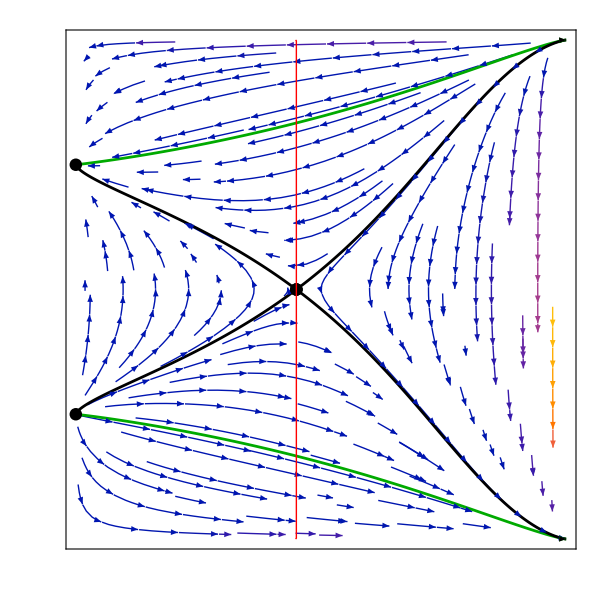

```mathematica
(*Plot the 2D phase space using StreamPlot*)
Show[StreamPlot[{deZ2D,deY2D},{Z,0,1},{Y,-1,1}],FFSPlot2D,FFSPlot2D2,CFSPlot2D,CFSPlot2D2,EinsteinFixedPoint2D,FPs2DZY,ZeroAccn,PhaseSpaceFormat2D]
```

```mathematica
(*Define the compact Friedmann equation to plot the trajectories with different values of Y0 for the phase space*)
trajZY[Y0_]:=Y^2/(1-Y^2)==
1/3+Z/(3*(1-Z))+RofZcrz[Z0,R0]/(3*(1-RofZcrz[Z0,R0]))-((Z*(1-Z0))/(Z0*(1-Z)))^(2/3)*(1/3+Z0/(3*(1-Z0))+R0/(3*(1-R0))-Y0^2/(1-Y0^2))
```

```mathematica
(*Plot trajectories with different values of Y0*)
```

```mathematica
trajPlotZY[1]=ContourPlot[Evaluate[trajZY[0.8]],{Z,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Magenta}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.035,0},1]]],Arrow[x]};
```

```mathematica
trajPlotZY[2]=ContourPlot[Evaluate[trajZY[0.8]],{Z,0,1},{Y,-0.999,0},PlotPoints->100,ContourStyle -> {{Magenta}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.035,0},1]]],Arrow[x]};
```

```mathematica
trajPlotZY[3]=ContourPlot[Evaluate[trajZY[0.4]],{Z,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Blue}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.035,0},1]]],Arrow[x]};
```

```mathematica
trajPlotZY[4]=ContourPlot[Evaluate[trajZY[0.4]],{Z,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Blue}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,0.035,0},1]]],Arrow[x]};
```

```mathematica
trajPlotZY[5]=ContourPlot[Evaluate[trajZY[0.05]],{Z,0.5,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.035,.035,0},1]]],Arrow[x]};
```

```mathematica
trajPlotZY[6]=ContourPlot[Evaluate[trajZY[0.05]],{Z,0,0.5},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,0,0,-0.035,0,0},1]]],Arrow[x]};
```

```mathematica
(*Put the trajectories into a table*)
trajTableZY=Table[trajPlotZY[i],{i,1,6}];
```

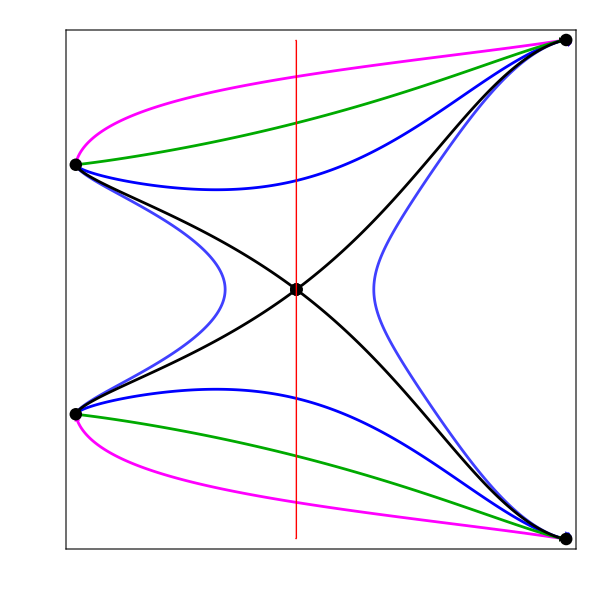

```mathematica
(*Show the 2D phase space*)
Show[trajTableZY,FFSPlot2D,FFSPlot2D2,CFSPlot2D,CFSPlot2D2,EinsteinFixedPoint2D,FPs2DZY,Singularities2D,ZeroAccn,PhaseSpaceFormat2D]
```